```mathematica
amd=FinancialData["NASDAQ:AMD","Close",All]
```

TimeSeries[…]

```mathematica
amdrat=Transpose[{
amd["Dates"][[;;-2]],
Ratios@amd["Values"]
}];
```

```mathematica
Length@amdrat
```

11865

```mathematica
Grid@
TakeLargestBy[amdrat,Last,20]
```

Tue 28 Jan 1975 00:00:00GMT-8. | 1.62561
Thu 21 Apr 2016 00:00:00GMT-8. | 1.5229
Mon 16 Dec 1974 00:00:00GMT-8. | 1.33261
Wed 9 Mar 1994 00:00:00GMT-8. | 1.26923
Fri 18 Oct 2002 00:00:00GMT-8. | 1.26136
Thu 9 Jan 1975 00:00:00GMT-8. | 1.25123
Tue 31 Dec 1974 00:00:00GMT-8. | 1.25123
Tue 25 Feb 1975 00:00:00GMT-8. | 1.25041
Thu 11 Jul 1974 00:00:00GMT-8. | 1.25
Mon 1 Oct 1973 00:00:00GMT-8. | 1.24431
Wed 16 Oct 2002 00:00:00GMT-8. | 1.24069
Wed 10 Nov 1999 00:00:00GMT-8. | 1.23757
Wed 19 Mar 1975 00:00:00GMT-8. | 1.23523
Wed 17 Jan 2001 00:00:00GMT-8. | 1.22635
Mon 29 Sep 2008 00:00:00GMT-8. | 1.22378
Tue 8 Oct 1974 00:00:00GMT-8. | 1.22176
Tue 31 Oct 1978 00:00:00GMT-8. | 1.2203
Wed 11 Nov 2009 00:00:00GMT-8. | 1.21805
Wed 7 Nov 1973 00:00:00GMT-8. | 1.21619
Tue 17 Apr 2001 00:00:00GMT-8. | 1.21087

```mathematica
Grid@
Table[{First@d,PercentForm[d-1]},{d,TakeLargestBy[amdrat,Last,20]}]
```

Tue 28 Jan 1975 00:00:00GMT-8. | {-100%+Tue 2800% Jan 197500% 00:00:00GMT-800%,62.56%}
Thu 21 Apr 2016 00:00:00GMT-8. | {-100%+Thu 2100% Apr 201600% 00:00:00GMT-800%,52.29%}
Mon 16 Dec 1974 00:00:00GMT-8. | {-100%+Mon 1600% Dec 197400% 00:00:00GMT-800%,33.26%}
Wed 9 Mar 1994 00:00:00GMT-8. | {-100%+Wed 900% Mar 199400% 00:00:00GMT-800%,26.92%}
Fri 18 Oct 2002 00:00:00GMT-8. | {-100%+Fri 1800% Oct 200200% 00:00:00GMT-800%,26.14%}
Thu 9 Jan 1975 00:00:00GMT-8. | {-100%+Thu 900% Jan 197500% 00:00:00GMT-800%,25.12%}
Tue 31 Dec 1974 00:00:00GMT-8. | {-100%+Tue 3100% Dec 197400% 00:00:00GMT-800%,25.12%}
Tue 25 Feb 1975 00:00:00GMT-8. | {-100%+Tue 2500% Feb 197500% 00:00:00GMT-800%,25.04%}
Thu 11 Jul 1974 00:00:00GMT-8. | {-100%+Thu 1100% Jul 197400% 00:00:00GMT-800%,25%}
Mon 1 Oct 1973 00:00:00GMT-8. | {-100%+Mon 100% Oct 197300% 00:00:00GMT-800%,24.43%}
Wed 16 Oct 2002 00:00:00GMT-8. | {-100%+Wed 1600% Oct 200200% 00:00:00GMT-800%,24.07%}
Wed 10 Nov 1999 00:00:00GMT-8. | {-100%+Wed 1000% Nov 199900% 00:00:00GMT-800%,23.76%}
Wed 19 Mar 1975 00:00:00GMT-8. | {-100%+Wed 1900% Mar 197500% 00:00:00GMT-800%,23.52%}
Wed 17 Jan 2001 00:00:00GMT-8. | {-100%+Wed 1700% Jan 200100% 00:00:00GMT-800%,22.64%}
Mon 29 Sep 2008 00:00:00GMT-8. | {-100%+Mon 2900% Sep 200800% 00:00:00GMT-800%,22.38%}
Tue 8 Oct 1974 00:00:00GMT-8. | {-100%+Tue 800% Oct 197400% 00:00:00GMT-800%,22.18%}
Tue 31 Oct 1978 00:00:00GMT-8. | {-100%+Tue 3100% Oct 197800% 00:00:00GMT-800%,22.03%}
Wed 11 Nov 2009 00:00:00GMT-8. | {-100%+Wed 1100% Nov 200900% 00:00:00GMT-800%,21.8%}
Wed 7 Nov 1973 00:00:00GMT-8. | {-100%+Wed 700% Nov 197300% 00:00:00GMT-800%,21.62%}
Tue 17 Apr 2001 00:00:00GMT-8. | {-100%+Tue 1700% Apr 200100% 00:00:00GMT-800%,21.09%}

```mathematica
Grid@
Table[{First@d,PercentForm[Last@d-1]},{d,TakeLargestBy[amdrat,Last,20]}]
```

Tue 28 Jan 1975 00:00:00GMT-8. | 62.56%
Thu 21 Apr 2016 00:00:00GMT-8. | 52.29%
Mon 16 Dec 1974 00:00:00GMT-8. | 33.26%
Wed 9 Mar 1994 00:00:00GMT-8. | 26.92%
Fri 18 Oct 2002 00:00:00GMT-8. | 26.14%
Thu 9 Jan 1975 00:00:00GMT-8. | 25.12%
Tue 31 Dec 1974 00:00:00GMT-8. | 25.12%
Tue 25 Feb 1975 00:00:00GMT-8. | 25.04%
Thu 11 Jul 1974 00:00:00GMT-8. | 25%
Mon 1 Oct 1973 00:00:00GMT-8. | 24.43%
Wed 16 Oct 2002 00:00:00GMT-8. | 24.07%
Wed 10 Nov 1999 00:00:00GMT-8. | 23.76%
Wed 19 Mar 1975 00:00:00GMT-8. | 23.52%
Wed 17 Jan 2001 00:00:00GMT-8. | 22.64%
Mon 29 Sep 2008 00:00:00GMT-8. | 22.38%
Tue 8 Oct 1974 00:00:00GMT-8. | 22.18%
Tue 31 Oct 1978 00:00:00GMT-8. | 22.03%
Wed 11 Nov 2009 00:00:00GMT-8. | 21.8%
Wed 7 Nov 1973 00:00:00GMT-8. | 21.62%
Tue 17 Apr 2001 00:00:00GMT-8. | 21.09%

```mathematica
BlockchainData[]
```

<|Type→Bitcoin,Name→BTC.main,Core→Bitcoin,Blocks→609859,LatestBlockHash→00000000000000000005a90ac870d919c5ea49e1b3f140cfb6ffc347fc5c3aad,MinimumFee→1000  sat|>

```mathematica
BlockchainData[]
```

<|Type→Bitcoin,Name→BTC.main,Core→Bitcoin,Blocks→609859,LatestBlockHash→00000000000000000005a90ac870d919c5ea49e1b3f140cfb6ffc347fc5c3aad,MinimumFee→1000  sat|>

```mathematica
BlockchainData["Blocks",BlockchainBase-> "Bitcoin"]
```

609859

```mathematica
BlockchainData[{"LowestGasPrice","AverageGasPrice","HighestGasPrice"},BlockchainBase-> "Ethereum"]
```

{0.0961559  Gwei,10.7289  Gwei,50.  Gwei}

```mathematica
BlockchainBlockData[1221,BlockchainBase-> "Bitcoin"]//Dataset
```

Dataset[<>]

```mathematica
BlockchainPut[{2,3,5,7,11}]
```

b0683d52366d768ae06820a0ca0222a7f3cff3fee78a5ac72e1f5d1ba88e18b8

```mathematica
BlockchainGet[Out[12]]
```

{2,3,5,7,11}

```mathematica
BlockchainData[BlockchainBase->{"Multichain","Wolfram"}]//Dataset
```

Dataset[<>]

```mathematica
BlockchainData[BlockchainBase->"Wolfram"]//Dataset
```

BlockchainData::bbase: Invalid BlockchainBase specification Wolfram.

Dataset`ExtractRawData::dataextr: Data extraction failed.

Dataset[$Failed]

```mathematica
BlockchainBlockData[100000,BlockchainBase->{"Multichain","Wolfram"}]//Dataset
```

Dataset[<>]

```mathematica
BlockchainBlockData[10000,BlockchainBase->{"Multichain","Wolfram"}]//Dataset
```

Dataset[<>]

```mathematica
BlockchainBlockData[1,BlockchainBase->{"Multichain","Wolfram"}]//Dataset
```

Dataset[<>]

```mathematica
First@BlockchainBlockData[1,BlockchainBase->{"Multichain","Wolfram"}]
```

005387447860ad03ab66895d9f34a0c0ba36670c7a01678457e8b6b8b5584ab2

```mathematica
BlockchainGet@Out@19
```

Missing[NotAvailable]

```mathematica
BlockchainGet["b465ec3c103af75d648d2793708d69e7f4715ca79023c4b8b170bc2349362960"]
```

-Graphics-

```mathematica
Options@BlockchainBase
```

{}

```mathematica
Integrate[(x^2-x)^2,{x,0,1}]
```

1/30

```mathematica
N[1/30]
```

0.0333333

```mathematica
Integrate[(x-x)^2,{x,0,1}]
```

0

```mathematica
Integrate[(f[x]-g[x])^2,{x,0,1}]
```

∫_0^1 (f[x]-g[x])^2 ⅆx

```mathematica
Integrate[(x^3-x^2)^2,{x,0,1}]
```

1/105

```mathematica
N[1/105]
```

0.00952381

```mathematica
Plot[
{x^2,x^3,(x^3-x^2)^2},
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",ImageSize->Full]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[{x^2,x^3,(x^3-x^2)^2},PlotTheme→Marketing,ColorFunction→DarkRainbow,ImageSize→Full]

```mathematica
Plot[
{x^2,x^3,(x^3-x^2)^2},{x,0,2},
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",ImageSize->Full]
```

-Graphics-

```mathematica
FullSimplify[Normalize@{x,D[f[x],x]}.Normalize@{x,D[f[x],{x,2}]},{x,f[x],f'[x],f''[x]}∈Reals]
```

(x^2+f'[x] f''[x])/(√((x^2+f'[x]^2) (x^2+f''[x]^2)))

```mathematica
With[{f=Function[x,x^3]},
(x^2+f'[x] f''[x])/(√((x^2+f'[x]^2) (x^2+f''[x]^2)))
]
```

(x^2+18 x^3)/(√37 √(x^2 (x^2+9 x^4)))

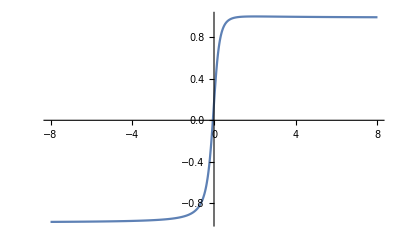

```mathematica
Plot[(x^2+18 x^3)/(√37 √(x^2 (x^2+9 x^4))),{x,-8,8}]
```

```mathematica
With[{f=Identity,g=Function[x,x^3]},
FullSimplify[
Normalize@{x,D[f[x],x]}.
Normalize@{x,D[g[x],x]}
,{x,f[x],f'[x],g[x],g'[x]}∈Reals]
]
```

(4 Abs[x])/(√((1+x^2) (1+9 x^2)))

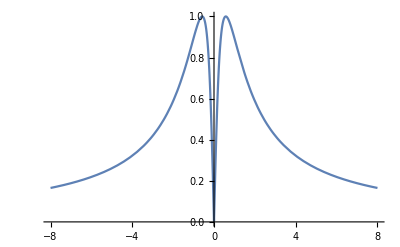

```mathematica
Plot[(4 Abs[x])/(√((1+x^2) (1+9 x^2))),{x,-8,8}]
```

```mathematica
FinancialData["NASDAQ:GOOG","Price"]
```

1 343.56 $

```mathematica
FinancialData["NASDAQ:GOOG","Ask"]
```

Missing[NotAvailable]

```mathematica
FinancialData["NASDAQ:GOOG","AskSize"]
```

Missing[NotAvailable]

```mathematica
FinancialData["NASDAQ:AAPL","AskSize"]
```

Missing[NotAvailable]

```mathematica
FinancialData["NASDAQ:AAPL","Ask"]
```

Missing[NotAvailable]

```mathematica
FinancialData["NASDAQ:AAPL","Close"]
```

284.27 $

```mathematica
FinancialData["NASDAQ:AAPL","Members"]
```

Missing[NotAvailable]

```mathematica
FinancialData["NASDAQ:AAPL","Average50Day"]
```

260.64 $

```mathematica
FinancialData["NASDAQ:AAPL","High52Week"]
```

284.89 $

```mathematica
FinancialData["NASDAQ:AAPL","Low52Week"]
```

142.00 $

```mathematica
DatePlus[Today[],Quantity[52,"Weeks"]]
```

DatePlus::date: Expression DateObject[{2019,12,26},Day,Gregorian,-8.][] cannot be interpreted as a date specification.

DatePlus[Day: Thu 26 Dec 2019[],52 wk]

```mathematica
Today[]
```

Day: Thu 26 Dec 2019[]

```mathematica
DatePlus[DateObject[{2017,1,1},"Day","Gregorian",-5.],Quantity[14,"Weeks"]]
```

Day: Sun 9 Apr 2017

```mathematica
DatePlus[Today,Quantity[52,"Weeks"]]
```

Day: Thu 24 Dec 2020

```mathematica
DatePlus[Today,-Quantity[52,"Weeks"]]
```

Day: Thu 27 Dec 2018

```mathematica
FinancialData["NASDAQ:AAPL","Close",{DatePlus[Today,-Quantity[52,"Weeks"]],Today}]
```

TimeSeries[…]

```mathematica
MinimumTimeIncrement[%51]
```

{1,Day}

```mathematica
TimeSeriesResample[%51]
```

TimeSeries[…]

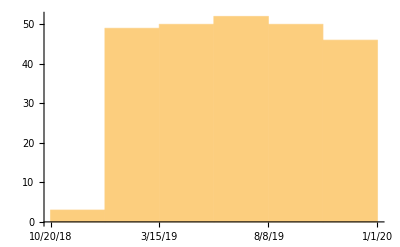

```mathematica
DateHistogram[%51]
```

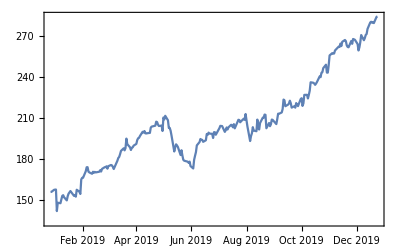

```mathematica
DateListPlot@TimeSeries[…]
```

```mathematica
Histogram[
Ratios[FinancialData["NASDAQ:AAPL","Close",{DatePlus[Today,-Quantity[52,"Weeks"]],Today}]["Values"]]
,PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
```

-Graphics-

```mathematica
Histogram[
Ratios[FinancialData["NASDAQ:AAPL","Close",{DatePlus[Today,-Quantity[52,"Weeks"]],Today}]["Values"]],
{.001}
,PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
```

-Graphics-

```mathematica
Ratios[FinancialData["NASDAQ:AAPL","Close",{DatePlus[Today,-Quantity[52,"Weeks"]],Today}]["Values"]]
```

{1.00051,1.00967,1.00114,0.900393,1.04269,0.997774,1.01906,1.01698,1.0032,0.990182,0.984963,1.02047,1.01222,1.00594,1.00616,0.977554,1.00404,0.992074,1.03314,0.990745,0.989635,1.06833,1.0072,1.00048,1.0284,1.01711,1.00034,0.981061,0.9969,0.994249,1.00862,0.995845,1.00364,0.997775,1.00299,1.00644,0.994361,1.01117,1.00728,1.00057,1.0031,0.990164,1.01051,1.00503,0.99818,0.994246,0.990775,1.03464,1.01124,1.00442,1.01112,1.01301,1.01021,0.992075,1.00874,1.03683,0.979292,0.987909,0.989668,1.00899,1.00133,1.00652,1.00679,1.01454,1.00685,1.00174,1.00669,1.01574,0.997001,1.00561,0.991676,0.999598,1.00181,1.0001,1.01947,1.00359,1.00329,1.01442,0.998458,0.990925,0.995226,1.00152,0.980744,1.04909,0.993492,1.01243,0.984557,0.973043,1.0002,0.989256,0.982363,0.941881,1.01583,1.01198,0.9956,0.994318,0.96873,1.01917,0.979528,0.98293,0.996159,0.995865,0.995231,1.00519,0.981884,0.98989,1.03658,1.01614,1.01468,1.02662,1.01278,1.01158,0.996817,0.999794,0.992738,1.00597,1.02352,0.997077,1.00804,0.996591,0.998994,0.984842,1.02163,0.9997,0.990888,1.01834,1.00585,1.00829,0.999119,0.979386,1.0061,1.00989,0.992718,1.00768,1.0094,0.99654,0.994377,1.01136,0.985072,1.02285,1.00782,0.999186,0.992093,1.00348,1.00934,0.995708,1.0204,0.978361,0.978842,0.947652,1.01893,1.01036,1.02206,0.988006,0.997463,1.04235,0.970235,0.995019,1.02359,1.01864,1.00005,1.01084,0.999154,0.95378,1.019,0.988716,1.00671,1.01693,0.998708,0.985436,1.01697,1.01955,0.999906,1.00427,1.01181,1.0318,0.997741,0.980568,1.00526,1.00364,1.00938,0.991875,0.985382,1.00455,0.995245,1.01539,0.994842,0.995134,1.02354,1.00277,0.974932,1.00849,1.02803,1.00022,0.988285,1.01172,1.01348,1.0266,0.998561,0.997668,0.995963,1.00388,1.0048,1.01734,0.997713,1.01342,1.00164,1.01232,1.01002,0.976872,0.999877,1.02261,1.02838,1.00657,0.998563,1.00043,1.00851,1.00274,1.00792,0.999085,1.00958,0.993081,1.01188,1.00504,0.996967,0.988359,0.995517,0.999122,1.01753,0.992191,1.01343,0.997797,0.988438,0.98217,1.00883,1.01467,1.01932,0.986,1.00584,1.00853,1.00255,1.01359,1.01712,1.00197,0.997611,1.001,0.997929,1.01632,1.00095}

```mathematica
Quartics[Out[60]]
```

Quartics[{1.00051,1.00967,1.00114,0.900393,1.04269,0.997774,1.01906,1.01698,1.0032,0.990182,0.984963,1.02047,1.01222,1.00594,1.00616,0.977554,1.00404,0.992074,1.03314,0.990745,0.989635,1.06833,1.0072,1.00048,1.0284,1.01711,1.00034,0.981061,0.9969,0.994249,1.00862,0.995845,1.00364,0.997775,1.00299,1.00644,0.994361,1.01117,1.00728,1.00057,1.0031,0.990164,1.01051,1.00503,0.99818,0.994246,0.990775,1.03464,1.01124,1.00442,1.01112,1.01301,1.01021,0.992075,1.00874,1.03683,0.979292,0.987909,0.989668,1.00899,1.00133,1.00652,1.00679,1.01454,1.00685,1.00174,1.00669,1.01574,0.997001,1.00561,0.991676,0.999598,1.00181,1.0001,1.01947,1.00359,1.00329,1.01442,0.998458,0.990925,0.995226,1.00152,0.980744,1.04909,0.993492,1.01243,0.984557,0.973043,1.0002,0.989256,0.982363,0.941881,1.01583,1.01198,0.9956,0.994318,0.96873,1.01917,0.979528,0.98293,0.996159,0.995865,0.995231,1.00519,0.981884,0.98989,1.03658,1.01614,1.01468,1.02662,1.01278,1.01158,0.996817,0.999794,0.992738,1.00597,1.02352,0.997077,1.00804,0.996591,0.998994,0.984842,1.02163,0.9997,0.990888,1.01834,1.00585,1.00829,0.999119,0.979386,1.0061,1.00989,0.992718,1.00768,1.0094,0.99654,0.994377,1.01136,0.985072,1.02285,1.00782,0.999186,0.992093,1.00348,1.00934,0.995708,1.0204,0.978361,0.978842,0.947652,1.01893,1.01036,1.02206,0.988006,0.997463,1.04235,0.970235,0.995019,1.02359,1.01864,1.00005,1.01084,0.999154,0.95378,1.019,0.988716,1.00671,1.01693,0.998708,0.985436,1.01697,1.01955,0.999906,1.00427,1.01181,1.0318,0.997741,0.980568,1.00526,1.00364,1.00938,0.991875,0.985382,1.00455,0.995245,1.01539,0.994842,0.995134,1.02354,1.00277,0.974932,1.00849,1.02803,1.00022,0.988285,1.01172,1.01348,1.0266,0.998561,0.997668,0.995963,1.00388,1.0048,1.01734,0.997713,1.01342,1.00164,1.01232,1.01002,0.976872,0.999877,1.02261,1.02838,1.00657,0.998563,1.00043,1.00851,1.00274,1.00792,0.999085,1.00958,0.993081,1.01188,1.00504,0.996967,0.988359,0.995517,0.999122,1.01753,0.992191,1.01343,0.997797,0.988438,0.98217,1.00883,1.01467,1.01932,0.986,1.00584,1.00853,1.00255,1.01359,1.01712,1.00197,0.997611,1.001,0.997929,1.01632,1.00095}]

```mathematica
Quartiles[Out[60]]
```

{0.995105,1.00274,1.01141}

```mathematica
Table[{f,f[Out[60]]}
,{f,{Mean,Median,Quartiles,Variance,TrimmedMean,StandardDeviation,MeanDeviation,QuartileDeviation,InterquartileRange,QuartileSkewness,TakeLargest[10],TakeSmallest[10],TrimmedVariance,GeometricMean,Skewness,Kurtosis,Composition[N,Entropy]}}]
```

{{Mean,1.00255},{Median,1.00274},{Quartiles,{0.995105,1.00274,1.01141}},{Variance,0.000273884},{TrimmedMean,1.00281},{StandardDeviation,0.0165495},{MeanDeviation,0.0115393},{QuartileDeviation,0.00815479},{InterquartileRange,0.0163096},{QuartileSkewness,0.0641389},{TakeLargest[10],{1.06833,1.04909,1.04269,1.04235,1.03683,1.03658,1.03464,1.03314,1.0318,1.0284}},{TakeSmallest[10],{0.900393,0.941881,0.947652,0.95378,0.96873,0.970235,0.973043,0.974932,0.976872,0.977554}},{TrimmedVariance,0.000113031},{GeometricMean,1.00241},{Skewness,-0.900675},{Kurtosis,9.96612},{N@*Entropy,5.51745}}

```mathematica
Grid@
Table[{f,f[Out[60]]}
,{f,{Mean,Median,Quartiles,Variance,TrimmedMean,StandardDeviation,MeanDeviation,QuartileDeviation,InterquartileRange,QuartileSkewness,TakeLargest[10],TakeSmallest[10],TrimmedVariance,GeometricMean,Skewness,Kurtosis,Composition[N,Entropy]}}]
```

Mean | 1.00255
Median | 1.00274
Quartiles | {0.995105,1.00274,1.01141}
Variance | 0.000273884
TrimmedMean | 1.00281
StandardDeviation | 0.0165495
MeanDeviation | 0.0115393
QuartileDeviation | 0.00815479
InterquartileRange | 0.0163096
QuartileSkewness | 0.0641389
TakeLargest[10] | {1.06833,1.04909,1.04269,1.04235,1.03683,1.03658,1.03464,1.03314,1.0318,1.0284}
TakeSmallest[10] | {0.900393,0.941881,0.947652,0.95378,0.96873,0.970235,0.973043,0.974932,0.976872,0.977554}
TrimmedVariance | 0.000113031
GeometricMean | 1.00241
Skewness | -0.900675
Kurtosis | 9.96612
N@*Entropy | 5.51745

```mathematica
Kurtosis[f[x]]
```

Kurtosis[f[x]]

```mathematica
pv==c/r
```

pv==c/r

```mathematica
100/(1+n)
```

100/(1+n)

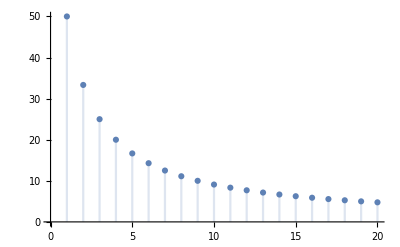

```mathematica
DiscretePlot[100/(1+n),{n,1,20}]
```

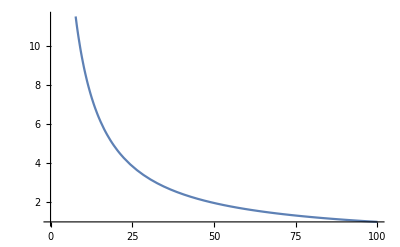

```mathematica
Plot[100/(1+n),{n,0,100}]
```

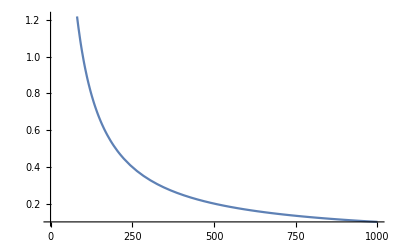

```mathematica
Plot[100/(1+n),{n,0,1000}]
```

```mathematica
TimeValue[Annuity[1000,10],.06,0]
```

7360.09

```mathematica
Annuity[1000,10]
```

Annuity[1000,10]

```mathematica
TimeValue[Annuity[100,10],.06,0]
```

736.009

```mathematica
Solve[TimeValue[Annuity[pmt,30,1/12],EffectiveInterest[.052,1/12],0]==200000,pmt]
```

{{pmt→1098.22}}

```mathematica
Solve[TimeValue[Annuity[pmt,3,1/12],.33,0]==5500,pmt]
```

{{pmt→230.061}}

```mathematica
Solve[TimeValue[Annuity[pmt,2,1/12],.33,0]==5500,pmt]
```

{{pmt→304.301}}

```mathematica
FinancialDerivative[]
```

{Altiplano,{American,Call},{American,Put},Annapurna,{AsianArithmetic,European,Call},{AsianArithmetic,European,Put},{AsianGeometric,European,Call},{AsianGeometric,European,Put},Atlas,{BarrierDownIn,American,Call},{BarrierDownIn,American,Put},{BarrierDownIn,European,Call},{BarrierDownIn,European,Put},{BarrierDownOut,American,Call},{BarrierDownOut,American,Put},{BarrierDownOut,European,Call},{BarrierDownOut,European,Put},{BarrierUpIn,American,Call},{BarrierUpIn,American,Put},{BarrierUpIn,European,Call},{BarrierUpIn,European,Put},{BarrierUpOut,American,Call},{BarrierUpOut,American,Put},{BarrierUpOut,European,Call},{BarrierUpOut,European,Put},{BinaryAsset,European,Call},{BinaryAsset,European,Put},{BinaryCash,European,Call},{BinaryCash,European,Put},{Chooser,European},{CompoundCall,European,Call},{CompoundCall,European,Put},{CompoundPut,European,Call},{CompoundPut,European,Put},{DoubleBarrierKnockIn,American,Call},{DoubleBarrierKnockIn,American,Put},{DoubleBarrierKnockIn,European,Call},{DoubleBarrierKnockIn,European,Put},{DoubleBarrierKnockOut,American,Call},{DoubleBarrierKnockOut,American,Put},{DoubleBarrierKnockOut,European,Call},{DoubleBarrierKnockOut,European,Put},{European,Call},{European,Put},Everest,{ExtendibleHolder,European,Call},{ExtendibleHolder,European,Put},{ExtendibleWriter,European,Call},{ExtendibleWriter,European,Put},{Future,European,Call},{Future,European,Put},Himalaya,{LookbackFixed,European,Call},{LookbackFixed,European,Put},{LookbackFloating,American,Call},{LookbackFloating,American,Put},{LookbackFloating,European,Call},{LookbackFloating,European,Put},{OneTouch,American,Call},{OneTouch,American,Put},{Perpetual,American,Call},{Perpetual,American,Put},{PerpetualLookback,Call},{PerpetualLookback,Put},{Power,European,Call},{Power,European,Put},{PowerCapped,European,Call},{PowerCapped,European,Put},{Powered,European,Call},{Powered,European,Put},{QuantoFixedExchange,American,Call},{QuantoFixedExchange,American,Put},{QuantoFixedExchange,European,Call},{QuantoFixedExchange,European,Put},{QuantoFixedStrike,American,Call},{QuantoFixedStrike,American,Put},{QuantoFixedStrike,European,Call},{QuantoFixedStrike,European,Put},{RainbowBest,American},{RainbowBest,European},{RainbowMax,American,Call},{RainbowMax,American,Put},{RainbowMax,European,Call},{RainbowMax,European,Put},{RainbowMin,American,Call},{RainbowMin,American,Put},{RainbowMin,European,Call},{RainbowMin,European,Put},{RainbowMoney,American},{RainbowMoney,European},{RainbowWorst,American},{RainbowWorst,European},Russian,{Spread,American,Call},{Spread,American,Put},{Spread,European,Call},{Spread,European,Put},{Vanilla,American,Call},{Vanilla,American,Put},{Vanilla,European,Call},{Vanilla,European,Put}}

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 50.00, "Expiration"->1},  {"InterestRate"-> 0.1, "Volatility" -> 0.5, "CurrentPrice"-> 50, "Dividend"->0.05}, {"Value", "Greeks"}]
```

{10.3649,{Delta→0.60577,Gamma→0.0142774,Rho→19.9236,Theta→-4.93963,Vega→17.8471}}

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 50.00, "Expiration"->1},  {"InterestRate"-> 0.1, "Volatility" -> 0.5, "CurrentPrice"-> 50}, {"Value", "Greeks"}]
```

{11.9634,{Delta→0.673645,Gamma→0.0144207,Rho→21.7188,Theta→-6.67852,Vega→18.0265}}

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 50.00, "Expiration"->1},  {"InterestRate"-> 0.1, "Volatility" -> 0.5, "CurrentPrice"-> 50, "Dividend"->0}, {"Value", "Greeks"}]
```

{11.9634,{Delta→0.673645,Gamma→0.0144207,Rho→21.7188,Theta→-6.67852,Vega→18.0265}}

```mathematica
FinancialDerivative[{"American","Call"}, {"StrikePrice"-> 50.00, "Expiration"->1},  {"InterestRate"-> 0.1, "Volatility" -> 0.5, "CurrentPrice"-> 50, "Dividend"->0}, {"Value", "Greeks"}]
```

{11.9355,{Delta→0.67422,Gamma→0.0144675,Rho→21.7028,Theta→-6.69766,Vega→18.1063}}

```mathematica
CountryData["UnitedStates","GiniIndex"]
```

0.45

```mathematica
CountryData["Netherlands","GiniIndex"]
```

0.309

```mathematica
CountryData["Sweden","GiniIndex"]
```

0.23

```mathematica
CountryData["HongKong","GiniIndex"]
```

0.533

```mathematica
CountryData["Mexico","GiniIndex"]
```

0.479

```mathematica
CountryData["Brazil","GiniIndex"]
```

0.567

```mathematica
Grid@
EntityValue[
EntityClass["Country",{"GiniIndex"->TakeLargest[10]}]
,{"Name","GiniIndex"}
]
```

Namibia | 0.591
Suriname | 0.576
Zambia | 0.571
Central African Republic | 0.562
Lesotho | 0.542
Brazil | 0.533
Botswana | 0.533
Belize | 0.533
Eswatini | 0.515
Saint Lucia | 0.512

```mathematica
CountryData["China","GiniIndex"]
```

0.47

```mathematica
Entity["SchoolDistrict"]
```

Entity[SchoolDistrict]

```mathematica
Entity["SchoolDistrict","SampleEntities"]
```

Entity[SchoolDistrict,SampleEntities]

```mathematica
EntityValue[
EntityClass["SchoolDistrict"{EntityProperty["SchoolDistrict","Population"]->TakeLargest[10]}]
,"EntityList"]
```

EntityValue[EntityClass[{SchoolDistrict (population→TakeLargest[10])}],EntityList]

```mathematica
EntityValue[
EntityClass["SchoolDistrict",{EntityProperty["SchoolDistrict","Population"]->TakeLargest[10]}]
,"EntityList"]
```

{Missing[UnknownProperty,{SchoolDistrict,EntityList}],Missing[UnknownProperty,{SchoolDistrict,EntityList}],Missing[UnknownProperty,{SchoolDistrict,EntityList}],Missing[UnknownProperty,{SchoolDistrict,EntityList}],Missing[UnknownProperty,{SchoolDistrict,EntityList}],Missing[UnknownProperty,{SchoolDistrict,EntityList}],Missing[UnknownProperty,{SchoolDistrict,EntityList}],Missing[UnknownProperty,{SchoolDistrict,EntityList}],Missing[UnknownProperty,{SchoolDistrict,EntityList}],Missing[UnknownProperty,{SchoolDistrict,EntityList}]}

```mathematica
EntityValue[
EntityClass["SchoolDistrict",{EntityProperty["SchoolDistrict","Population"]->TakeLargest[10]}]
,"EntityAssociation"]
```

<|New York City School District→{supervisory union,2.92861×10^11 $,Missing[NotAvailable],3044559000 $,48388000 $,0 $,0 $,58660000 $,{New York City},{40.7137,-74.0056},175673000 $,0 $,448671000 $,14936045000 $,15384716000 $,0 $,694900000 $,4068503000 $,591836000 $,90586000 $,120,0 $,Missing[NotAvailable],24597709000 $,2047926000 $,2050988000 $,10600597000 $,Missing[NotAvailable],2. people,21023695000 $,0 $,10254583000 $,8375172000 $,81 people,1534225000 $,23. people,25. people,6249461000 $,0. people,231338 households,584229 people},8,Hawaii Department of Education→{1}|>
 |  |  |  |

```mathematica
EntityValue[
EntityClass["SchoolDistrict",{EntityProperty["SchoolDistrict","Population"]->TakeLargest[10]}]
,{"Name","Population"}]
```

{{New York City School District,8560072 people},{Los Angeles Unified School District,4708406 people},{City of Chicago School District 299,2722548 people},{Miami-Dade County Public School District,2702602 people},{Clark County School District,2112436 people},{Broward County School District,1890416 people},{Philadelphia School District,1569657 people},{Houston Independent School District,1458616 people},{Palm Beach County School District,1426772 people},{Hawaii Department of Education,1421658 people}}

```mathematica
Grid@
ReverseSortBy[
EntityValue[
EntityClass["SchoolDistrict",{EntityProperty["SchoolDistrict","Population"]->TakeLargest[10]}]
,{"Name","Population"}]
,Last]
```

New York City School District | 8560072 people
Los Angeles Unified School District | 4708406 people
City of Chicago School District 299 | 2722548 people
Miami-Dade County Public School District | 2702602 people
Clark County School District | 2112436 people
Broward County School District | 1890416 people
Philadelphia School District | 1569657 people
Houston Independent School District | 1458616 people
Palm Beach County School District | 1426772 people
Hawaii Department of Education | 1421658 people

```mathematica
Quantity[23, "Bitcoins"]
```

23 ฿